## (*++++ ---- The Discrete Crawler ---- ++++ *)

```mathematica
(*--Author: Patricio A. Vela--*)

(*--Created: January 15, 2002--*)
(*--Modified: June 18, 2016--*)
```

## (*--Initialization--*)

### (*--Load Libraries--*)

```mathematica
(*--Load libraries and define objects--*)
<<ivamatica/defpackages.m;
LoadPackages[TANGENTS+TPRINCIPAL]
DoneLoading

(* Additional basic math functions. *)
<<ivamatica/Basic/extras.m

(* For dealing with equations of motions. *)
<<ivamatica/Dynamics/equations.m
<<ivamatica/Dynamics/averaging.m

(* Lagrangian mechanics. *)
<<ivamatica/Mechanics/constraints.m
<<ivamatica/Mechanics/kinematics.m
<<ivamatica/Mechanics/lagrangian.m

(* For creating visual movie output. *)
<<ivamatica/Graphics/anim.m
```

UpSetDelayed::write: Tag Integer in oInit[Binary, len_Integer] is Protected.

UpSetDelayed::write: Tag Integer in oInit[Binary, len_Integer, val_Integer] is Protected.

UpSetDelayed::write: Tag Integer in oSet[Binary[b_], val_Integer] is Protected.

General::stop: Further output of UpSetDelayed :: write will be suppressed during this calculation.

Loaded Euclidean package 
Loaded Fiber Bundles package 
Loaded Manifolds package 
Loaded Vectors package 
Loaded Tangents package 
Loaded Tangent Fiber Bundles package 
Loaded Tangent Manifolds package 
Loaded Lie Groups package 
Loaded Tangent Lie Groups package 
Loaded Principal Bundles package 
Loaded Tangent Principal Bundles package

Removed package loading variables.

```mathematica
M = Euclidean;
TM = TEuclidean;

G=SE2;
𝔤 = se2;
SuperStar[𝔤] = dse2;
TG = TSE2;
tG = SE2xse2;
dG = SE2xdse2;

Q=ExSE2;
TQ = TExTSE2;

CO = Configuration;
```

```mathematica
Off[General::spell1];
Off[General::spell];
```

### (*--Configuration space and other variables--*)

```mathematica
g = oInit[G, x, y, θ];
dimG=gDim[g];

g' = oInit[Vector, Table[ gLocal[g][[i]]' , {i, dimG}] ];
gdot = oInit[Vector, Table[OverDot[gLocal[g][[i]]],{i,dimG}]];

gp = oInit[TG , g, g'];

r = oInit[M, {ψ, Right, Left}];
r' = oInit[Vector, Table[ gLocal[r][[i]]' , {i, Length[r]}]];
rdot = oInit[Vector, Table[OverDot[r[[i]]],{i,Length[r]}]];
dimM = gDim[r];

ξ = oInit[𝔤, { ξ1 , ξ2, ξ3}];
e = oInit[𝔤, { e1, e2, e3}];
q =  oInit[Q, r, g]
qp = oInit[TQ, r, g, r', g']
```

Group  Fiber {x, y, θ} with base {ψ, Right, Left}

Tangent Vector {{ψ'}, {x', y', θ'}} of principal fiber bundle at the point {{ψ, Right, Left}, {x, y, θ}}

### (*--Constants of the discrete crawler--*)

```mathematica
doSim=1;
If[doSim==1,(*--Mass of rotating element--*)pmR=1;
(*--Mass of body--*)pmB=4;
(*--Total mass of crawler--*)pM=pmB+pmR;
(*--Distance from center to peg--*)pd=1/6;
(*--Inertia of the rotor--*)pJr=1/24;
(*--Inertia of the body--*)pJb=1/2 pM pd^2;
(*--Total inertia of crawler--*)pJt=pJb+pJr;
,
Clear[ pmR, pmB, pM, pd, pJr, pJb];
pJt = pJb + pJr];
```

```mathematica
pJr/(pJt + pJb)
```

3/13

## (*--Equations of Motion--*)

### (*--Local Form of the Principal Connection--*)

```mathematica
r𝒜 = oInit[𝔤, pJr/(pJt + pM pd^2){0, -pd, 1}];
l𝒜 = oInit[𝔤, pJr/(pJt + pM pd^2){0, pd, 1}];
```

### (*--Lagrangian of the System--*)

```mathematica
L[qp_] := Module[{lr,lrp, lg, lgp,lag} ,

lr = gLocal[gBase[qp]];
lg = gLocal[gGroup[qp]];
lrp = gLocal[gBaseVector[qp]];
lgp = gLocal[gGroupVector[qp]];

lag = 1/2 pM ( ( lgp[[1]])^2+ (lgp[[2]])^2) + 1/2 pJb (lgp[[3]])^2 ;
lag += 1/2 pJr ( lgp[[3]] + lrp[[1]])^2;
lag
]
```

```mathematica
ℓ = cReduce[ L[qp], gp, ξ]
Subscript[ℓ, cR] = Simplify[ℓ /. Table[ gLocal[ξ][[i]] -> gLocal[r𝒜][[i]] gLocal[r'][[1]]   , {i, gDim[ξ]}]]
Subscript[ℓ, cL] =  Simplify[ℓ /. Table[ gLocal[ξ][[i]] -> gLocal[l𝒜][[i]] gLocal[r'][[1]]   , {i, gDim[ξ]}]]
```

5/2 (ξ1^2+ξ2^2)+(5 ξ3^2)/144+1/48 (ξ3+ψ')^2

(ψ')^2/32

(ψ')^2/32

## (*--Simulations--*)

### (*--The Different Gaits--*)

#### (*--Forward Gait--*)

```mathematica
ψ̄ = 0; ψ̃ = π; 
ω = 1;
ϵ = 1;
Τ=2 π ϵ/ω;
```

```mathematica
Mod[6.3, 2π]
```

0.0168147

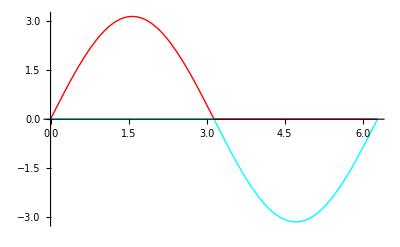

```mathematica
v1[t_] :=   ψ̄ + If[ Mod[t, 2π]≤ π , 1, 0] ψ̃ Sin[t];
v2[t_] :=  ψ̄ + If[ Mod[t, 2π]≤  π , 0, 1] ψ̃ Sin[t];
Plot[{v1[t], v2[t]}, {t, 0, 2 π}, PlotStyle-> {RGBColor[1,0,0], RGBColor[0,1,1]}] 
xover = Τ/2;
```

#### (*--Rotate Gait--*)

```mathematica
ψ̄ = π; ψ̃ = -π; 
ω = 1;
ϵ = 1/6;
Τ=2 π ϵ/ω;
```

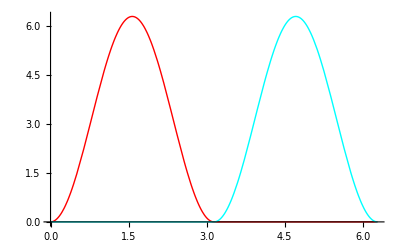

```mathematica
f[t_] := ψ̄ + ψ̃ Cos[2 t];
v1[t_] :=   If[ Mod[t,2π]≤ π , 1, 0]   ( ψ̄ +ψ̃ Cos[2t]);
v2[t_] :=   If[ Mod[t,2π]≤  π , 0, 1]  ( ψ̄ + ψ̃ Cos[2t]);
Plot[{v1[t], v2[t]}, {t, 0, 2 π}, PlotStyle-> {RGBColor[1,0,0], RGBColor[0,1,1]}] 
xover = Τ/2;
```

#### (*--Forward Gait withTurning--*)

```mathematica
ψ̄ = π/4; ψ̃ = π; 
ω = 1;
ϵ = 1/6;
Τ=2 π ϵ/ω;
```

4.94827

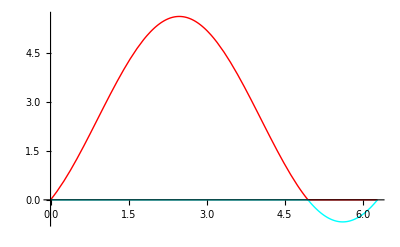

```mathematica
xover=t /.FindRoot[  ψ̄+ Sin[t - ArcSin[ ψ̄]]== 0, {t,(π + ArcSin[ψ̄]),0,2π}]
v1[t_] := Which[ Mod[t, 2π]≤ xover, 1,Mod[t,2π] ≤  2π, 0]   ψ̃( ψ̄+ Sin[t - ArcSin[ ψ̄]]);
v2[t_] :=  Which[ Mod[t,2π]≤  xover , 0,  Mod[t,2π]≤  2π, 1]   ψ̃( ψ̄+ Sin[t - ArcSin[ ψ̄]]);
Plot[{v1[t], v2[t]}, {t, 0, 2 π}, PlotStyle-> {RGBColor[1,0,0], RGBColor[0,1,1]}]
```

#### (*--Sideways Gait--*)

```mathematica
ψ̄ = 0; ψ̃ = π; 
ω = 1;
ϵ = 1/2;
Τ = 2 π ϵ / ω;
```

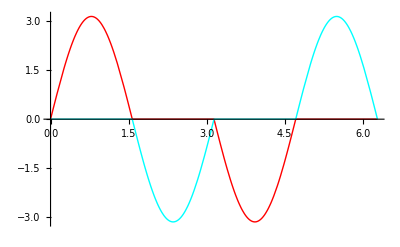

```mathematica
v1[t_] := Which[ Mod[t,2π] ≤  π/2 , 1, Mod[t,2π] ≤  π, 0, Mod[t,2π] ≤ (3 π)/2,-1, Mod[t,2π] ≤ 2 π, 0]  *  ψ̃ Sin[2 t];
v2[t_] := Which[ Mod[t,2π] ≤  π/2 , 0,  Mod[t,2π]≤  π, 1,  Mod[t,2π]≤ (3 π)/2,0, Mod[t,2π] ≤ 2 π, -1]  *  ψ̃ Sin[2 t];
Plot[{v1[t], v2[t]}, {t, 0, 2 π}, PlotStyle-> {RGBColor[1,0,0], RGBColor[0,1,1]}]
```

#### (*--Simulation proper--*)

```mathematica
t0 = 0;
t1 = 2Τ;
```

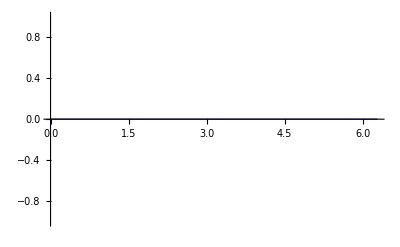
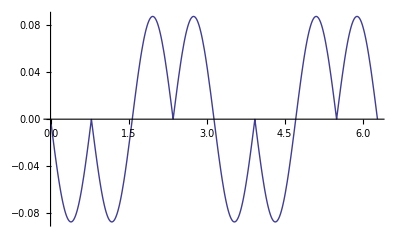
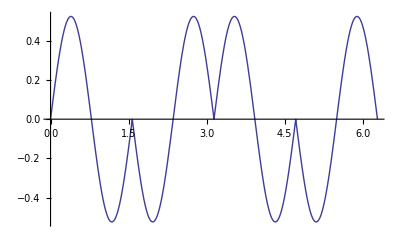

```mathematica
𝒜[tt_] := v1[tt] r𝒜 + v2[tt] l𝒜;
Table[ Plot[gLocal[𝒜[(ω t)/ϵ]][[i]],{t,0,2 Τ}],{i,dimG}]
```

```mathematica
gsol = NDSolve[-𝒜[ (ω t)/ϵ] , oInit[G,{0,0,0}],g,{t,t0, t1}, MaxSteps -> 10000]
rft[t_] := {Integrate[v1[tt] + v2[tt] ,{tt,0,Mod[t, Τ]}] , If[v1[t] ≠ 0, 1,0], If[v2[t] ≠ 0, 1, 0]};
gft[t_] := Flatten[Table[ gLocal[g][[i]][t] /. gsol , {i, 1, gDim[g]}]];
qft[t_] := Join[ rft[(ω t)/ϵ], gft[t]];
gdes[t_] := oInit[G,{0,0,0}];
```

NDSolve::nlnum: The function value {0., 0., -0.0886378\ Null} is not a list of numbers with dimensions {3} at {t, x[t], y[t], θ[t], NDSolve`s$2556[t]} = {3.16278, 0.0227161, 0.0000783005, 0.000469652, 1}.

{{x→InterpolatingFunction[{{0.,3.12116}},<>],y→InterpolatingFunction[{{0.,3.12116}},<>],θ→InterpolatingFunction[{{0.,3.12116}},<>]}}

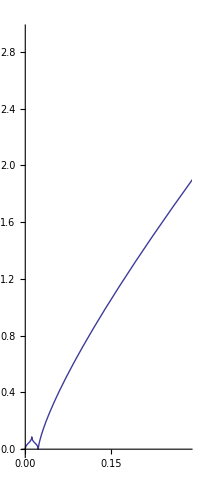

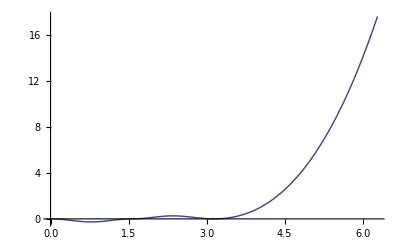

```mathematica
ParametricPlot[{gft[t][[1]],gft[t][[2]]},{t,t0, t1}, AspectRatio->Automatic]
Plot[ gft[t][[3]], {t, t0, t1}]
(*Plot[Evaluate[D[v1[(ω t)/ϵ]+v2[(ω t)/ϵ],t]],{t,t0, t1}]*)
(*Plot[ rft[t][[1]], {t, t0, t1}]*)
```

### (*--Lie Group Control--*)

```mathematica
despath = 2;
```

```mathematica
Which[despath == 1, k = {3, 8, 0}, despath == 2, k = {3, 8,0}];
errF[G[gerr_]] := Module[ {α1, α2} , 
  α1 =k[[2]] gerr[[2]];
α2 = (- k[[1]] ArcTanH[ gerr[[2]], -gerr[[1]] ] - k[[3]] gerr[[3]]);
{α1, α2}
]
```

```mathematica
Clear[α, xover, gsol];
Remove[gdes];
```

```mathematica
ω=1;
ϵ=1/3;
Τ = (2 π ϵ)/ω;

f[t_] := ( α[[1]]Sin[t]+1/2 α[[2]]( 1 - Cos[2t]));
v1[t_] := If[Mod[t,2 π] ≤ xover, 1,0] f[t];
v2[t_] := If[Mod[t, 2 π] ≤ xover,0,1]f[t];

𝒜[tt_] := v1[tt] r𝒜 + v2[tt] l𝒜;
```

```mathematica
Which[despath == 1, {g0=oInit[G,{-1,5, π/5}];
gdes[t_] := oInit[G, {0,0,0}]};,
despath == 2, {g0=oInit[G,{-0.2,0.3,π/12}];
 gdes[t_] := oInit[G, {√8/100 t, √8/100 t, ArcTan[(√8)/100, -(√8)/100]}]}];
errv = N[errF[Inverse[g0]·gdes[0]]]
```

{-2.73233,-0.97861}

```mathematica
gcurr=g0;
gflow=Append[{},gcurr];

αflow = {};
xflow = {};
rflow = {};

maxsteps=40;
t0 = 0; t1 = maxsteps * Τ;

For[cnt=1,cnt<=maxsteps,cnt++,
α = errF[Inverse[gcurr] ·gdes[cnt*Τ]];
Which[α[[1]] > 8, α[[1]] = 8, α[[1]] < -8, α[[1]] = -8];
Which[α[[2]] > π/2, α[[2]] = π/2, α[[2]] < -π/2, α[[2]] = -π/2];
xover=t /.FindRoot[f[t] == 0, {t,π ,0,2 π}];
gsol[cnt] =  NDSolve[ -𝒜[(ω t)/ϵ] , gcurr,g,{t,0, Τ}]
(*gsol1[cnt]=G[fDSolve,-rA f[t],{x,y,θ},gcurr,{t,t0,xover}];
gsol2[cnt]=G[fDSolve,-lA f[t+xover],{x,y,θ},Flatten[Table[g[[i]][xover]/.gsol1[cnt],{i,1,G[fDim]}]],{t,0,t1-xover}];*);
gcurr=oInit[G,Flatten[Table[gLocal[g][[i]][Τ]/.gsol[cnt],{i,1,gDim[g]}]]];
gflow=Append[gflow,gcurr];
αflow = Append[αflow, α];
xflow = Append[xflow, xover];
rflow = Append[rflow, ∫f[(ω t)/ϵ] ⅆt];
];
```

```mathematica
N[{gcurr, gdes[t1]}] 
Inverse[gcurr] ·gdes[cnt*Τ]
```

{(2.20471
2.2551
2.23014),(2.36954
2.36954
-0.785398)}

(0.0000103934
-0.283492
-3.01554)

```mathematica
gft[t_]:=Module[{nt,tt},nt=Floor[t/Τ]+1;
If[nt≤maxsteps,tt=t-Floor[t/Τ] Τ,nt=maxsteps;
tt=Τ;];
Table[(gLocal[g][[i]][tt]/.gsol[nt])[[1]],{i,1,dimG}]
];

Clear[dist, err];
rft[time_] := Module[{nt, tt}, nt = Floor[time/Τ] + 1;
If[nt≤maxsteps,tt=time-Floor[time/Τ] Τ,nt=maxsteps;
tt=Τ;];
Which[ tt ≤ ϵ/ω xflow[[nt]] , {rflow[[nt]] /. {t -> tt}, 1, 0} , True, {rflow[[nt]] /. {t -> tt},0, 1}]
];

qft[t_] := Join[rft[t], gft[t]];
```

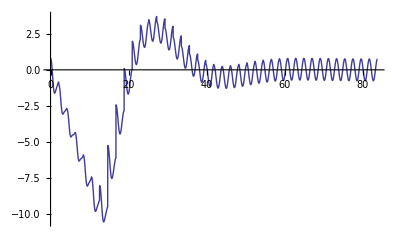

```mathematica
Plot[rft[t][[1]],{t,t0,t1}]
```

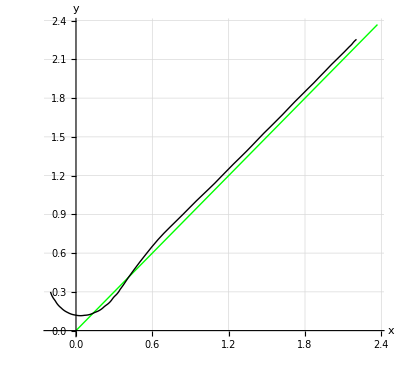

```mathematica
ParametricPlot[{{gLocal[gdes[t]][[1]],gLocal[gdes[t]][[2]]},{gft[t][[1]],gft[t][[2]]} },{t,t0, t1},AxesLabel->{"x","y"},PlotRange->All, GridLines->Automatic, PlotStyle->{RGBColor[0,1,0], RGBColor[0,0,0]}]
```

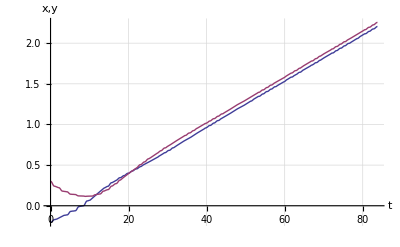

```mathematica
Plot[{gft[t][[1]], gft[t][[2]]}, {t, t0, t1}, AxesLabel->{"t", "x,y"},PlotRange->All, GridLines->Automatic]
```

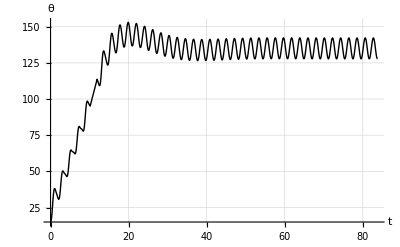

```mathematica
Plot[gft[t][[3]]*180/π, {t,t0, t1},AxesLabel->{"t", "θ"}, PlotRange->All, GridLines->Automatic, PlotStyle -> {RGBColor[0,1,0], RGBColor[0,0,0]}]
```

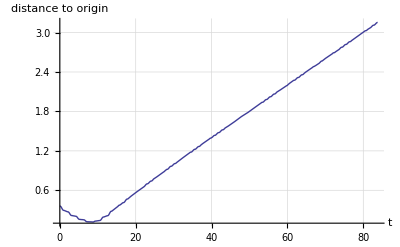

```mathematica
Plot[Abs[gft[t][[1]] + ⅈ gft[t][[2]]], {t, t0, t1}, AxesLabel-> {"t", "distance to origin"},PlotRange->All, GridLines->Automatic]
```

### (*--Stabilization Using Forward Gait And Rotate Gait; Old--*)

```mathematica
(*--Needs more work.  An error function is wrong.--*)
```

```mathematica
(*--Error functionn for the position and orientation--*)
(*--Use errF--*)
```

```mathematica
errR[cp_] := Module[{ev, xv, dv}, dv = {-Sin[cp[[3]]],Cos[cp[[3]]]};
xv = {cp[[1]], cp[[2]]};
ev = xv/Abs[cp[[1]] + ⅈ cp[[2]]];
(-xv).dv];
 
errθ[cp_, sgn_] := Module[{ev, xv, dv}, dv = {-Sin[cp[[3]]],Cos[cp[[3]]]};
xv = {cp[[1]], cp[[2]]};
ev = xv/Abs[cp[[1]] + ⅈ cp[[2]]];
sgn (dv[[1]] ev[[2]] - dv[[2]] ev[[1]])]

errF[cp_] := Module[{ev, xv, dv, sgn, er1,er2}, dv = {-Sin[cp[[3]]],Cos[cp[[3]]]};
xv = {cp[[1]], cp[[2]]};
ev = xv/Abs[cp[[1]] + ⅈ cp[[2]]];
er1 = xv.dv;
sgn =  Which[er1 == 0, 1, True, Sign[er1]];
er2 = ArcSin[(dv[[1]] ev[[2]] - dv[[2]] ev[[1]])];
{er1, er2, sgn}]
```

```mathematica
Clear[err,dist, xover, gsol];
Remove[gdes];
```

```mathematica
ω=1;
ϵ=1/3;
Τ = (2 π ϵ)/ω;

f[t_] := ( dist Sin[t]+1/2 err( 1 - Cos[2t]));
v1[t_] :=  If[ Mod[t,2 π] ≤ xover, 1, 0] f[t];
v2[t_] := If[Mod[t, 2 π] ≤  xover, 0, 1]f[t];

𝒜[tt_] := v1[tt] r𝒜 + v2[tt] l𝒜;
```

```mathematica
g0={-1,5,π/5};
errv = errF[g0]
```

{√(5/8-(√5)/8)+5/4 (1+√5),-ArcSin[5 √(1/26 (5/8-(√5)/8))-(1+√5)/(4 √26)],1}

```mathematica
gcurr=g0;
gflow=Append[{},gcurr];
gdes[t_] := {0,0,0};

eflow={};
dflow={};
xflow = {};

maxsteps=400;
t0 = 1; t1 = maxsteps * Τ;

For[cnt=1,cnt<=maxsteps,cnt++,
errv = errF[gcurr];
dist =-3 errv[[1]];
err =-3 errv[[3]]errv[[2]];
Which[err > π/2, err = π, err < -π/2, err = -π];
Which[dist > π/2, dist = 3/2 π, dist < -π/2, dist = -3/2 π];
xover=t /.FindRoot[f[(ω t)/ϵ] == 0, {t,ϵ/ω(π + ψ̄),0,Τ}];
gsol[cnt] =  oNDSolve[g, -𝒜[(ω t)/ϵ] , oInit[G,gcurr],{t,0, Τ}]
(*gsol1[cnt]=G[fDSolve,-rA f[t],{x,y,θ},gcurr,{t,t0,xover}];
gsol2[cnt]=G[fDSolve,-lA f[t+xover],{x,y,θ},Flatten[Table[g[[i]][xover]/.gsol1[cnt],{i,1,G[fDim]}]],{t,0,t1-xover}];*);
gcurr=Flatten[Table[gLocal[g][[i]][Τ]/.gsol[cnt],{i,1,gDim[g]}]];
gflow=Append[gflow,gcurr];
eflow=Append[eflow,err];
dflow=Append[dflow,dist];
xflow = Append[xflow, xover];
];
```

ReplaceAll::reps: oNDSolve[TagBox[( TagBox[GridBox[{{ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

FindRoot::nlnum: The function value 0.`  is not a list of numbers with dimensions {1} at {t} = {1.0472}.

General::stop: Further output of FindRoot :: nlnum will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$IterationLimit::itlim: Iteration limit of 4096 exceeded.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$IterationLimit::itlim: Iteration limit of 4096 exceeded.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$IterationLimit::itlim: Iteration limit of 4096 exceeded.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$IterationLimit::itlim: Iteration limit of 4096 exceeded.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$IterationLimit::itlim: Iteration limit of 4096 exceeded.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$IterationLimit::itlim: Iteration limit of 4096 exceeded.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$IterationLimit::itlim: Iteration limit of 4096 exceeded.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$IterationLimit::itlim: Iteration limit of 4096 exceeded.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$IterationLimit::itlim: Iteration limit of 4096 exceeded.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$IterationLimit::itlim: Iteration limit of 4096 exceeded.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$IterationLimit::itlim: Iteration limit of 4096 exceeded.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$IterationLimit::itlim: Iteration limit of 4096 exceeded.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$IterationLimit::itlim: Iteration limit of 4096 exceeded.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$IterationLimit::itlim: Iteration limit of 4096 exceeded.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$IterationLimit::itlim: Iteration limit of 4096 exceeded.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$IterationLimit::itlim: Iteration limit of 4096 exceeded.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$IterationLimit::itlim: Iteration limit of 4096 exceeded.

General::stop: Further output of $IterationLimit :: itlim will be suppressed during this calculation.

ReplaceAll::reps: oNDSolve[TagBox[( TagBox[GridBox[{{ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

ReplaceAll::reps: oNDSolve[TagBox[( TagBox[GridBox[{{ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

ReplaceAll::reps: oNDSolve[TagBox[( TagBox[GridBox[{{ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

FindRoot::nlnum: The function value {0.  - 3.67394×10^-16\ Hold[Cos[ReplaceAll[« 2 »]]\ (y[« 1 »]/. oNDSolve[« 4 »]) - 1.\ (x[« 1 »]/. oNDSolve[« 4 »])\ Sin[ReplaceAll[« 2 »]]]} is not a list of numbers with dimensions {1} at {t} = {1.0472}.

ReplaceAll::reps: {FindRoot[f[ω\ t/ϵ] == 0, {t, ϵ\ (π + ψ _)/ω, 0, Τ}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

ReplaceAll::reps: oNDSolve[TagBox[( TagBox[GridBox[{{ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

ReplaceAll::reps: oNDSolve[TagBox[( TagBox[GridBox[{{ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

ReplaceAll::reps: oNDSolve[TagBox[( TagBox[GridBox[{{ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

ReplaceAll::reps: oNDSolve[TagBox[( TagBox[GridBox[{{ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

ReplaceAll::reps: oNDSolve[TagBox[( TagBox[GridBox[{{ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

FindRoot::nlnum: The function value {0.  - 3.67394×10^-16\ Hold[Cos[ReplaceAll[« 2 »]]\ (y[« 1 »]/. oNDSolve[« 4 »]) - 1.\ (x[« 1 »]/. oNDSolve[« 4 »])\ Sin[ReplaceAll[« 2 »]]]} is not a list of numbers with dimensions {1} at {t} = {1.0472}.

ReplaceAll::reps: {FindRoot[f[ω\ t/ϵ] == 0, {t, ϵ\ (π + ψ _)/ω, 0, Τ}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

ReplaceAll::reps: oNDSolve[TagBox[( TagBox[GridBox[{{ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

ReplaceAll::reps: oNDSolve[TagBox[( TagBox[GridBox[{{ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

ReplaceAll::reps: oNDSolve[TagBox[( TagBox[GridBox[{{ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

ReplaceAll::reps: oNDSolve[TagBox[( TagBox[GridBox[{{ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

ReplaceAll::reps: oNDSolve[TagBox[( TagBox[GridBox[{{ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

FindRoot::nlnum: The function value {0.  - 3.67394×10^-16\ Hold[Cos[ReplaceAll[« 2 »]]\ (y[« 1 »]/. oNDSolve[« 4 »]) - 1.\ (x[« 1 »]/. oNDSolve[« 4 »])\ Sin[ReplaceAll[« 2 »]]]} is not a list of numbers with dimensions {1} at {t} = {1.0472}.

ReplaceAll::reps: {FindRoot[f[ω\ t/ϵ] == 0, {t, ϵ\ (π + ψ _)/ω, 0, Τ}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

ReplaceAll::reps: oNDSolve[TagBox[( TagBox[GridBox[{{ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

ReplaceAll::reps: oNDSolve[TagBox[( TagBox[GridBox[{{ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

ReplaceAll::reps: oNDSolve[TagBox[( TagBox[GridBox[{{ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

ReplaceAll::reps: oNDSolve[TagBox[( TagBox[GridBox[{{ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

ReplaceAll::reps: oNDSolve[TagBox[( TagBox[GridBox[{{ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

FindRoot::nlnum: The function value {0.  - 3.67394×10^-16\ Hold[Cos[ReplaceAll[« 2 »]]\ (y[« 1 »]/. oNDSolve[« 4 »]) - 1.\ (x[« 1 »]/. oNDSolve[« 4 »])\ Sin[ReplaceAll[« 2 »]]]} is not a list of numbers with dimensions {1} at {t} = {1.0472}.

ReplaceAll::reps: {FindRoot[f[ω\ t/ϵ] == 0, {t, ϵ\ (π + ψ _)/ω, 0, Τ}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

ReplaceAll::reps: oNDSolve[TagBox[( TagBox[GridBox[{{ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

ReplaceAll::reps: oNDSolve[TagBox[( TagBox[GridBox[{{ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

ReplaceAll::reps: oNDSolve[TagBox[( TagBox[GridBox[{{ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

ReplaceAll::reps: oNDSolve[TagBox[( TagBox[GridBox[{{ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

ReplaceAll::reps: oNDSolve[TagBox[( TagBox[GridBox[{{ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

ReplaceAll::reps: oNDSolve[TagBox[( TagBox[GridBox[{{ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

FindRoot::nlnum: The function value {0.  - 3.67394×10^-16\ Hold[Cos[ReplaceAll[« 2 »]]\ (y[« 1 »]/. oNDSolve[« 4 »]) - 1.\ (x[« 1 »]/. oNDSolve[« 4 »])\ Sin[ReplaceAll[« 2 »]]]} is not a list of numbers with dimensions {1} at {t} = {1.0472}.

ReplaceAll::reps: {FindRoot[f[ω\ t/ϵ] == 0, {t, ϵ\ (π + ψ _)/ω, 0, Τ}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

ReplaceAll::reps: oNDSolve[TagBox[( TagBox[GridBox[{{ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

ReplaceAll::reps: oNDSolve[TagBox[( TagBox[GridBox[{{ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

ReplaceAll::reps: oNDSolve[TagBox[( TagBox[GridBox[{{ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

ReplaceAll::reps: oNDSolve[TagBox[( TagBox[GridBox[{{ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

ReplaceAll::reps: oNDSolve[TagBox[( TagBox[GridBox[{{ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

FindRoot::nlnum: The function value {0.  - 3.67394×10^-16\ Hold[Cos[ReplaceAll[« 2 »]]\ (y[« 1 »]/. oNDSolve[« 4 »]) - 1.\ (x[« 1 »]/. oNDSolve[« 4 »])\ Sin[ReplaceAll[« 2 »]]]} is not a list of numbers with dimensions {1} at {t} = {1.0472}.

ReplaceAll::reps: {FindRoot[f[ω\ t/ϵ] == 0, {t, ϵ\ (π + ψ _)/ω, 0, Τ}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

ReplaceAll::reps: oNDSolve[TagBox[( TagBox[GridBox[{{ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

ReplaceAll::reps: oNDSolve[TagBox[( TagBox[GridBox[{{ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

ReplaceAll::reps: oNDSolve[TagBox[( TagBox[GridBox[{{ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

ReplaceAll::reps: oNDSolve[TagBox[( TagBox[GridBox[{{ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

ReplaceAll::reps: oNDSolve[TagBox[( TagBox[GridBox[{{ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

FindRoot::nlnum: The function value {0.  - 3.67394×10^-16\ Hold[Cos[ReplaceAll[« 2 »]]\ (y[« 1 »]/. oNDSolve[« 4 »]) - 1.\ (x[« 1 »]/. oNDSolve[« 4 »])\ Sin[ReplaceAll[« 2 »]]]} is not a list of numbers with dimensions {1} at {t} = {1.0472}.

ReplaceAll::reps: {FindRoot[f[ω\ t/ϵ] == 0, {t, ϵ\ (π + ψ _)/ω, 0, Τ}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

ReplaceAll::reps: oNDSolve[TagBox[( TagBox[GridBox[{{ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

ReplaceAll::reps: oNDSolve[TagBox[( TagBox[GridBox[{{ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

ReplaceAll::reps: oNDSolve[TagBox[( TagBox[GridBox[{{ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

ReplaceAll::reps: oNDSolve[TagBox[( TagBox[GridBox[{{ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

ReplaceAll::reps: oNDSolve[TagBox[( TagBox[GridBox[{{ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

$Aborted

```mathematica
gft[t_]:=Module[{nt,tt},nt=Floor[t/Τ]+1;
If[nt≤maxsteps,tt=t-Floor[t/Τ] Τ,nt=maxsteps;
tt=Τ;];
Table[(gLocal[g][[i]][tt]/.gsol[nt])[[1]],{i,1,dimG}]
];

Clear[dist, err];
rft[t_] := Module[{nt, tt}, nt = Floor[t/Τ] + 1;
If[nt≤maxsteps,tt=t-Floor[t/Τ] Τ,nt=maxsteps;
tt=Τ;];
Which[tt ≤ xflow[[nt]], {f[tt] /. {err -> eflow[[nt]], dist -> dflow[[nt]]}, 1, 0} , True,

{f[tt] /. {err -> eflow[[nt]], dist -> dflow[[nt]]}, 0, 1}]]

qft[t_] := Join[rft[t], gft[t]];
```

```mathematica
ParametricPlot[{gft[t][[1]],gft[t][[2]]},{t,t0, t1},AxesLabel->{"x","y"},PlotRange->All, GridLines->Automatic]
```

```mathematica
Plot[{gft[t][[1]], gft[t][[2]]}, {t, t0, t1}, AxesLabel->{"t", "x,y"},PlotRange->All, GridLines->Automatic]
```

```mathematica
Plot[gft[t][[3]], {t,t0, t1},AxesLabel->{"t", "theta"}, PlotRange->All, GridLines->Automatic]
```

```mathematica
Plot[Abs[gft[t][[1]] + ⅈ gft[t][[2]]], {t, t0, t1}, AxesLabel-> {"t", "distance to origin"},PlotRange->All, GridLines->Automatic]
```

### (*--Trajectory Tracking Using Forward Gait With Turning; Old--*)

```mathematica
Clear[err, dist, xover, gsol];
```

```mathematica
ψ̄ = err; ψ̃ =dist; 
ω = 1;
ϵ =1/4;
Τ=2 π ϵ/ω;
```

```mathematica
N[Τ]
```

```mathematica
f[t_] :=ψ̃ ( ψ̄+ Sin[t - ArcSin[ ψ̄]]);
v1[t_] :=  If[ Mod[t,2 π] ≤ xover, 1, 0] f[t];
v2[t_] := If[Mod[t, 2 π] ≤  xover, 0, 1]f[t];

𝒜[tt_] := v1[tt] r𝒜 + v2[tt] l𝒜;
```

```mathematica
f[t]
```

```mathematica
CalcDist[gdes_,gcur_]:=Module[{dx,dy},dx=gdes[[1]]-gcur[[1]];
dy=gdes[[2]]-gcur[[2]];
Sign[Cos[ArcTan[dy,dx]]] Abs[dx+ⅈ dy]];
```

```mathematica
g0={0,0,0};
gdes[t_] := {1/100 t, 2/200 t, 0};
gcurr=g0;
gflow=Append[{},gcurr];

eflow={};
dflow={};
xflow = {};

maxsteps=80;

kMp = 4; kMv = 3;
kTp= 4; kTv = 3;

For[cnt=1,cnt≤maxsteps,cnt++,
dist = CalcDist[gdes[cnt*Τ], gcurr];
If[cnt == 1,
terr =kMp(gdes[cnt*Τ][[1]] - gcurr[[1]])+kMv(gdes[cnt*Τ][[1]] - gcurr[[1]])/Τ,
terr = kTp (gdes[cnt*Τ][[1]] - gcurr[[1]])+ kTv ((gdes[cnt*Τ][[1]]-gdes[(cnt-1)*Τ][[1]])/Τ - (gcurr[[1]] - gflow[[Length[gflow]-1]][[1]])/Τ)];
err = terr;
Which[err > π/4, err = π/4, err < -π/4, err = -π/4];
Which[dist > 3, dist = 3, dist < -3, dist = -3];
xover=t /.FindRoot[f[(ω t)/ϵ] == 0, {t,ϵ/ω(π +ArcSin[ψ̄]),0,Τ}];
gsol[cnt] =  oNDSolve[g, -𝒜[(ω t)/ϵ] , oInit[G,gcurr],{t,0, Τ}];
(*gsol1[cnt]=G[fDSolve,-rA f[t],{x,y,θ},gcurr,{t,t0,xover}];
gsol2[cnt]=G[fDSolve,-lA f[t+xover],{x,y,θ},Flatten[Table[g[[i]][xover]/.gsol1[cnt],{i,1,dimG}]],{t,0,t1-xover}];*)
gcurr=Flatten[Table[gLocal[g][[i]][Τ]/.gsol[cnt],{i,1,dimG}]];
gflow=Append[gflow,gcurr];
eflow=Append[eflow,err];
dflow=Append[dflow,dist];
xflow = Append[xflow, xover];
];
```

```mathematica
eflow
```

```mathematica
dflow
```

```mathematica
f[t]
```

```mathematica
gft[t_]:=Module[{nt,tt},nt=Floor[t/Τ]+1;
If[nt≤maxsteps,tt=t-Floor[t/Τ] Τ,nt=maxsteps;
tt=Τ;];
Table[(gLocal[g][[i]][tt]/.gsol[nt])[[1]],{i,1,dimG}]
];
```

```mathematica
ParametricPlot[{{gft[t][[1]],gft[t][[2]]},{gdes[t][[1]], gdes[t][[2]]}},{t,0,maxsteps*Τ},PlotRange->All, GridLines->Automatic, AxesLabel->{"x","y"}]
```

```mathematica
Plot[{gft[t][[1]],gft[t][[2]]},{t,0,maxsteps*Τ},PlotRange->All]
```

```mathematica
Plot[gft[t][[3]],{t,0,maxsteps*Τ}]
```

```mathematica
Plot[f[(ω t)/ϵ],{t,0,Τ}]
```

## (*--Animating the Biped--*)

### (*-- Definitions. --*)

```mathematica
bodylen = pd + pd/5;
corndist = bodylen * √2;
pegrad = pd/5;
rotlen = pd/2;

Which[despath==1,{XWIN = {3.1, 4.1};YWIN = {1.1, 6.1};},
despath == 2,{XWIN = {1.1, 4.1};YWIN = {1.1, 4.1};}];
GRDX= {-10,10};
GRDY = { -10, 10};
GSTP = 1;
CSTP = 1.5;
XLen = bodylen;
BipedParams = {AspectRatio->Automatic,Axes->{False,False}, Frame->True};

gBiped[q_] := Module[{x, y, θ, gfx, angles, r1, r2, r3, xcent, ycent},
x = q[[dimM+1]]; y = q[[dimM+2]]; θ = q[[dimM+3]];

angles = {-(3π)/4, -π/4, π/4, (3 π)/4,-(3π)/4};
gfx= {Line[Table[ {x  - corndist Cos[θ + angles[[i]]], y - corndist Sin[θ + angles[[i]]]}, {i, Length[angles]}]]};
gfx = Append[gfx, If[  q[[2]] == 1, Disk[ {x + pd Cos[θ] , y +pd Sin[θ]}, pegrad],Disk[ {x -pd Cos[θ] , y -  pd Sin[θ]}, pegrad] ] ];
gfx = Append[gfx, {Thickness[0.01],Line[{{x + rotlen Cos[θ + q[[1]]], y + rotlen Sin[θ + q[[1]]]},{x -rotlen Cos[θ + q[[1]]], y - rotlen Sin[θ + q[[1]]]}}] }];
gfx = Append[gfx,fMakeGrid[GRDX, GRDY, GSTP]];
gfx = Append[gfx,Disk[despt, 0.05]];
Graphics[gfx,AspectRatio -> Automatic, PlotRange->{{x -XWIN,x+XWIN},{y-YWIN,y+YWIN}}]
]

gBiped[q_, gd_, params___] := Module[{x, y, θ, gfx, angles, r1, r2, r3, plot1},
x = q[[dimM+1]]; y = q[[dimM+2]]; θ = q[[dimM+3]];

angles = {-(3π)/4, -π/4, π/4, (3 π)/4,-(3π)/4};
gfx= {Line[Table[ {x  - corndist Cos[θ + angles[[i]]], y - corndist Sin[θ + angles[[i]]]}, {i, Length[angles]}]]};
gfx = Append[gfx, If[  q[[2]] == 1, {Disk[ {x + pd Cos[θ] , y + pd Sin[θ]}, pegrad],Circle[ {x - pd Cos[θ] , y -  pd Sin[θ]}, pegrad]},{Circle[ {x + pd Cos[θ] , y + pd Sin[θ]}, pegrad],Disk[ {x - pd Cos[θ] , y -  pd Sin[θ]}, pegrad] }] ];
gfx = Append[gfx, {Thickness[0.01],Line[{{x + rotlen Cos[θ + q[[1]]], y + rotlen Sin[θ + q[[1]]]},{x -rotlen Cos[θ + q[[1]]], y - rotlen Sin[θ + q[[1]]]}}] }];
gfx = Append[gfx,fMakeGrid[GRDX, GRDY, GSTP]];

plot1 = {gPosition[G[gd]·oInit[G, {-1/4 XLen , 0, 0}]], gPosition[ G[gd] ·oInit[G, {1/4 XLen , 0, 0}]]};
gfx = Append[gfx, {RGBColor[0,0,1], Line[plot1]}];
gfx=Append[gfx,{RGBColor[0,0,1],Disk[gPosition[G[gd]],1/40 XLen]}];
plot1 = {gPosition[G[gd]· oInit[G,{0,1/2 XLen,0}]], gPosition[ G[gd] ·oInit[G, {0 ,- 1/4 XLen, 0}]]};gfx = Append[gfx, {RGBColor[0,0,1], Line[plot1]}];

gfx = Append[gfx,{RGBColor[0,0,1],Disk[{gd[[1]], gd[[2]]}, 1/8 XLen]}];
xcent =0*Max[xcent, CSTP Quotient[gd[[1]], CSTP]];
ycent =0*Max[ycent, CSTP Quotient[gd[[2]], CSTP]];
Graphics[gfx,Join[{ PlotRange->{{xcent-XWIN[[1]],xcent +XWIN[[2]]},{ycent-YWIN[[1]],ycent+YWIN[[2]]}}},params]]
]
```

### (*-- Visualization Outputs. --*)

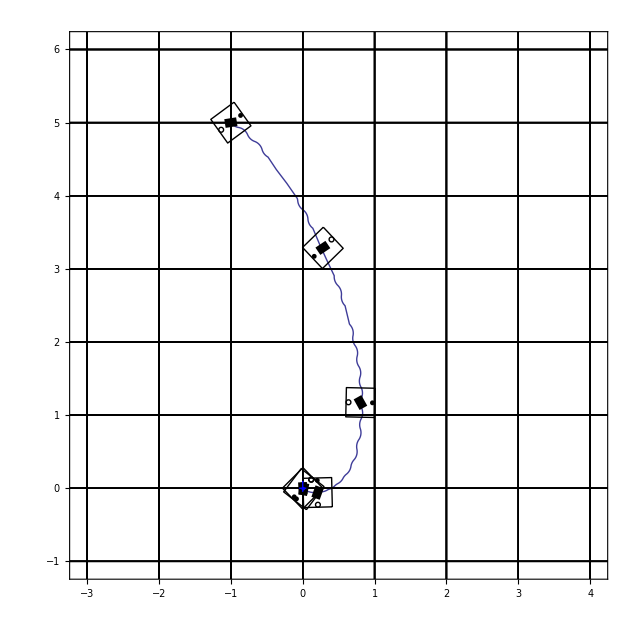

```mathematica
pplot =ParametricPlot[{gft[t][[1]],gft[t][[2]]},{t,t0, t1}, {DisplayFunction->Identity}]; 
snaps  =Table[gBiped[qft[t], gLocal[gdes[t]], BipedParams] , {t,t0, t1, (t1-t0)/5.25}];
stills = Table[ snaps[[i]][[1]], {i, 1, Length[snaps]}];
Graphics[{{RGBColor[1,0,0],pplot[[1]]},stills}, snaps[[1]][[2]]]//Show
```

## (*--Saving to file--*)

```mathematica
stf = t1;
tg = Table[ Join[ {t} , N[rft[t]] , gft[t], N[gLocal[gdes[t]]] ] , {t, 0, stf,0.05}];
```

```mathematica
(*Export["/home/pvela/Matlab/examples/dp02/dp02_tt.dat", tg]*)
```

Export::nodir: Directory "/home/pv33/Matlab/examples/dp02/" does not exist.

OpenWrite::noopen: Cannot open "/home/pv33/Matlab/examples/dp02/dp02_tt.dat".

$Failed

```mathematica
qft[0]
```

{8/3,1,0,-1.,5.,0.628319}

```mathematica
Animate[ gBiped[qft[t],gLocal[gdes[t]]], {t,t0,t1, Τ/10}]
```

```mathematica
dp2movie = Table[gBiped[qft[t], gLocal[gdes[t]]], {t, 0,70,0.1}];
Length[dp2movie]
```

701

```mathematica
useInternal = false;
If [useInternal,Export["test.avi",dp2movie], 
fMakeMovie["/home/pvela/tex/talks/BioInspLocomotion/video/walker/mtmp/","biped_stab",dp2movie]];
```